Используем для примера очистку от сезонности ряда по ЖКХ, MoM.

```mathematica
SetDirectory[NotebookDirectory[]];
<<"x13.m"
```

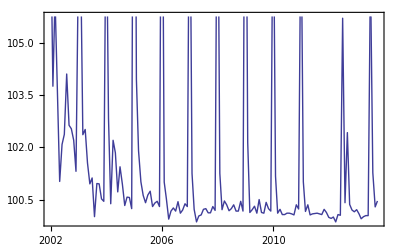

```mathematica
S=Rest@Import["GKH.xlsx",{"Data",1}];
DateListPlot[S,Joined->True]
```

```mathematica
S
```

{{{2002,1,1,0,0,0.},108.75},{{2002,2,1,0,0,0.},103.75},{{2002,3,1,0,0,0.},106.28},{{2002,4,1,0,0,0.},103.62},{{2002,5,1,0,0,0.},101.02},{{2002,6,1,0,0,0.},102.08},{{2002,7,1,0,0,0.},102.37},{{2002,8,1,0,0,0.},104.1},{{2002,9,1,0,0,0.},102.63},{{2002,10,1,0,0,0.},102.53},{{2002,11,1,0,0,0.},102.2},{{2002,12,1,0,0,0.},101.31},{{2003,1,1,0,0,0.},107.16},{{2003,2,1,0,0,0.},107.31},{{2003,3,1,0,0,0.},102.36},{{2003,4,1,0,0,0.},102.51},{{2003,5,1,0,0,0.},101.55},{{2003,6,1,0,0,0.},100.95},{{2003,7,1,0,0,0.},101.12},{{2003,8,1,0,0,0.},100.01},{{2003,9,1,0,0,0.},100.96},{{2003,10,1,0,0,0.},100.95},{{2003,11,1,0,0,0.},100.52},{{2003,12,1,0,0,0.},100.45},{{2004,1,1,0,0,0.},109.57},{{2004,2,1,0,0,0.},102.82},{{2004,3,1,0,0,0.},100.38},{{2004,4,1,0,0,0.},102.2},{{2004,5,1,0,0,0.},101.84},{{2004,6,1,0,0,0.},100.72},{{2004,7,1,0,0,0.},101.44},{{2004,8,1,0,0,0.},100.94},{{2004,9,1,0,0,0.},100.33},{{2004,10,1,0,0,0.},100.57},{{2004,11,1,0,0,0.},100.56},{{2004,12,1,0,0,0.},100.24},{{2005,1,1,0,0,0.},119.37},{{2005,2,1,0,0,0.},103.95},{{2005,3,1,0,0,0.},101.9},{{2005,4,1,0,0,0.},101.01},{{2005,5,1,0,0,0.},100.62},{{2005,6,1,0,0,0.},100.41},{{2005,7,1,0,0,0.},100.63},{{2005,8,1,0,0,0.},100.74},{{2005,9,1,0,0,0.},100.3},{{2005,10,1,0,0,0.},100.4},{{2005,11,1,0,0,0.},100.45},{{2005,12,1,0,0,0.},100.3},{{2006,1,1,0,0,0.},113.81},{{2006,2,1,0,0,0.},101.},{{2006,3,1,0,0,0.},100.53},{{2006,4,1,0,0,0.},99.94},{{2006,5,1,0,0,0.},100.17},{{2006,6,1,0,0,0.},100.26},{{2006,7,1,0,0,0.},100.17},{{2006,8,1,0,0,0.},100.44},{{2006,9,1,0,0,0.},100.11},{{2006,10,1,0,0,0.},100.2},{{2006,11,1,0,0,0.},100.38},{{2006,12,1,0,0,0.},100.3},{{2007,1,1,0,0,0.},111.07},{{2007,2,1,0,0,0.},101.25},{{2007,3,1,0,0,0.},100.22},{{2007,4,1,0,0,0.},99.86},{{2007,5,1,0,0,0.},100.03},{{2007,6,1,0,0,0.},100.06},{{2007,7,1,0,0,0.},100.22},{{2007,8,1,0,0,0.},100.24},{{2007,9,1,0,0,0.},100.12},{{2007,10,1,0,0,0.},100.12},{{2007,11,1,0,0,0.},100.3},{{2007,12,1,0,0,0.},100.19},{{2008,1,1,0,0,0.},111.83},{{2008,2,1,0,0,0.},101.25},{{2008,3,1,0,0,0.},100.21},{{2008,4,1,0,0,0.},100.46},{{2008,5,1,0,0,0.},100.35},{{2008,6,1,0,0,0.},100.18},{{2008,7,1,0,0,0.},100.24},{{2008,8,1,0,0,0.},100.35},{{2008,9,1,0,0,0.},100.17},{{2008,10,1,0,0,0.},100.17},{{2008,11,1,0,0,0.},100.45},{{2008,12,1,0,0,0.},100.17},{{2009,1,1,0,0,0.},114.35},{{2009,2,1,0,0,0.},102.14},{{2009,3,1,0,0,0.},100.13},{{2009,4,1,0,0,0.},100.21},{{2009,5,1,0,0,0.},100.31},{{2009,6,1,0,0,0.},100.11},{{2009,7,1,0,0,0.},100.5},{{2009,8,1,0,0,0.},100.13},{{2009,9,1,0,0,0.},100.11},{{2009,10,1,0,0,0.},100.42},{{2009,11,1,0,0,0.},100.24},{{2009,12,1,0,0,0.},100.17},{{2010,1,1,0,0,0.},110.07},{{2010,2,1,0,0,0.},101.17},{{2010,3,1,0,0,0.},100.11},{{2010,4,1,0,0,0.},100.22},{{2010,5,1,0,0,0.},100.07},{{2010,6,1,0,0,0.},100.07},{{2010,7,1,0,0,0.},100.11},{{2010,8,1,0,0,0.},100.11},{{2010,9,1,0,0,0.},100.09},{{2010,10,1,0,0,0.},100.06},{{2010,11,1,0,0,0.},100.35},{{2010,12,1,0,0,0.},100.23},{{2011,1,1,0,0,0.},109.05},{{2011,2,1,0,0,0.},101.01},{{2011,3,1,0,0,0.},100.16},{{2011,4,1,0,0,0.},100.35},{{2011,5,1,0,0,0.},100.06},{{2011,6,1,0,0,0.},100.09},{{2011,7,1,0,0,0.},100.1},{{2011,8,1,0,0,0.},100.11},{{2011,9,1,0,0,0.},100.09},{{2011,10,1,0,0,0.},100.07},{{2011,11,1,0,0,0.},100.22},{{2011,12,1,0,0,0.},100.13},{{2012,1,1,0,0,0.},99.99},{{2012,2,1,0,0,0.},99.96},{{2012,3,1,0,0,0.},100.},{{2012,4,1,0,0,0.},99.86},{{2012,5,1,0,0,0.},100.07},{{2012,6,1,0,0,0.},100.05},{{2012,7,1,0,0,0.},105.7},{{2012,8,1,0,0,0.},100.41},{{2012,9,1,0,0,0.},102.42},{{2012,10,1,0,0,0.},100.36},{{2012,11,1,0,0,0.},100.2},{{2012,12,1,0,0,0.},100.15},{{2013,1,1,0,0,0.},100.21},{{2013,2,1,0,0,0.},100.09},{{2013,3,1,0,0,0.},99.95},{{2013,4,1,0,0,0.},100.01},{{2013,5,1,0,0,0.},100.04},{{2013,6,1,0,0,0.},100.04},{{2013,7,1,0,0,0.},107.01},{{2013,8,1,0,0,0.},101.27},{{2013,9,1,0,0,0.},100.29},{{2013,10,1,0,0,0.},100.46}}

```mathematica
FileNameJoin[{$TemporaryDirectory,"mmax13"}]
```

C:\Users\iav\AppData\Local\Temp\mmax13

```mathematica
sa=x13[S];
```

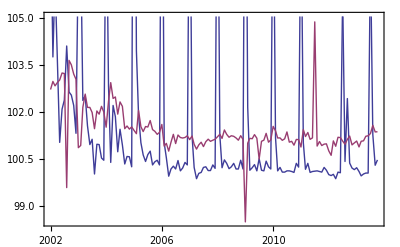

```mathematica
DateListPlot[{S,sa},Joined->True]
```

It’s a tricky time series cause the seasonality has changed somewhat in 2012 due to the election compaign and posponing of the rate hikes till summer.

```mathematica
Quiet@Check[deleteBraces@ToString[{"seasonal/2012.01/"}],""]
```

seasonal/2012.01/

```mathematica
Quiet@Check[deleteBraces@ToString[OptionValue[x13,Outliers]],""]
```

```mathematica
sa=x13[S,Outliers->{"seasonal/2012.01/"}]
```

```mathematica
DateListPlot[{S,sa},Joined->True]
```

-Graphics-

```mathematica
ToString[({asf,adfa})]
```

```mathematica
"{asf, adfa}"
```

```mathematica
{asf, adfa}
```

{asf,adfa}

```mathematica
""
```

```mathematica
"{}"
```

```mathematica
$Aborted
```

```mathematica
OptionValue[x13,Output]
```

e2

```mathematica
Sequence@@Options[x13]
```

Sequence[ARIMA→True,Mode→auto,Frequency→Month,Output→e2,Outliers→{}]

```mathematica
runx13[{},Sequence@Options[x13]]
```

First::first: {} has a length of zero and no first element.

DateString::fmtarg: DateString[{}, {"Year", ".", "Month"}] specifies the date format twice.

Last::nolast: {} has a length of zero and no last element.

DateString::fmtarg: DateString[{}, {"Year", ".", "Month"}] specifies the date format twice.

First::first: {} has a length of zero and no first element.

DatePlus::date: Argument {} cannot be interpreted as a date.

DateString::arg: Argument DatePlus[{}, {3, "Year"}] cannot be interpreted as a date or time input or as a date string format.

StringJoin::string: String expected at position 2 in "series{\n  title=\"Title\"\n  start=" <> « 1 » <> "\n  data=()\n}\nspectrum{\n  savelog=peaks\t\n}\ntransform{\n  function=auto\n  savelog=autotransform  \n}\n\nregression {\n\tvariables = ()\n\n}\n\n\nautomdl{}\n\noutlier{\n  method=addone\n  critical=3.7\n}\nx11{\n  print=none\n  save=(e2)}\n\n".

{{{2002,1,1},102.709},{{2002,2,1},102.967},{{2002,3,1},102.826},{{2002,4,1},102.933},{{2002,5,1},103.014},{{2002,6,1},103.237},{{2002,7,1},103.22},{{2002,8,1},99.5752},{{2002,9,1},103.639},{{2002,10,1},103.497},{{2002,11,1},103.205},{{2002,12,1},103.036},{{2003,1,1},100.851},{{2003,2,1},100.922},{{2003,3,1},102.14},{{2003,4,1},102.563},{{2003,5,1},102.137},{{2003,6,1},102.137},{{2003,7,1},101.974},{{2003,8,1},101.457},{{2003,9,1},102.024},{{2003,10,1},101.921},{{2003,11,1},102.171},{{2003,12,1},101.99},{{2004,1,1},101.505},{{2004,2,1},102.334},{{2004,3,1},102.929},{{2004,4,1},102.424},{{2004,5,1},102.472},{{2004,6,1},101.923},{{2004,7,1},102.313},{{2004,8,1},102.172},{{2004,9,1},101.458},{{2004,10,1},101.544},{{2004,11,1},101.444},{{2004,12,1},101.515},{{2005,1,1},101.403},{{2005,2,1},101.298},{{2005,3,1},102.039},{{2005,4,1},101.522},{{2005,5,1},101.366},{{2005,6,1},101.527},{{2005,7,1},101.512},{{2005,8,1},101.718},{{2005,9,1},101.428},{{2005,10,1},101.374},{{2005,11,1},101.277},{{2005,12,1},101.34},{{2006,1,1},101.593},{{2006,2,1},100.9},{{2006,3,1},100.989},{{2006,4,1},100.741},{{2006,5,1},101.025},{{2006,6,1},101.277},{{2006,7,1},100.982},{{2006,8,1},101.256},{{2006,9,1},101.175},{{2006,10,1},101.159},{{2006,11,1},101.176},{{2006,12,1},101.231},{{2007,1,1},101.108},{{2007,2,1},101.222},{{2007,3,1},100.958},{{2007,4,1},100.805},{{2007,5,1},100.94},{{2007,6,1},101.025},{{2007,7,1},100.886},{{2007,8,1},101.042},{{2007,9,1},101.123},{{2007,10,1},101.054},{{2007,11,1},101.09},{{2007,12,1},101.12},{{2008,1,1},101.199},{{2008,2,1},101.278},{{2008,3,1},101.147},{{2008,4,1},101.417},{{2008,5,1},101.277},{{2008,6,1},101.184},{{2008,7,1},101.232},{{2008,8,1},101.214},{{2008,9,1},101.162},{{2008,10,1},101.09},{{2008,11,1},101.234},{{2008,12,1},101.115},{{2009,1,1},98.4795},{{2009,2,1},100.995},{{2009,3,1},101.149},{{2009,4,1},101.137},{{2009,5,1},101.268},{{2009,6,1},101.153},{{2009,7,1},100.486},{{2009,8,1},101.055},{{2009,9,1},101.091},{{2009,10,1},101.308},{{2009,11,1},101.026},{{2009,12,1},101.099},{{2010,1,1},101.532},{{2010,2,1},101.39},{{2010,3,1},101.161},{{2010,4,1},101.162},{{2010,5,1},101.086},{{2010,6,1},101.135},{{2010,7,1},101.354},{{2010,8,1},101.027},{{2010,9,1},101.054},{{2010,10,1},100.931},{{2010,11,1},101.114},{{2010,12,1},101.108},{{2011,1,1},100.872},{{2011,2,1},101.429},{{2011,3,1},101.207},{{2011,4,1},101.336},{{2011,5,1},101.117},{{2011,6,1},101.164},{{2011,7,1},104.87},{{2011,8,1},100.902},{{2011,9,1},101.048},{{2011,10,1},100.919},{{2011,11,1},100.964},{{2011,12,1},100.973},{{2012,1,1},100.749},{{2012,2,1},100.607},{{2012,3,1},101.067},{{2012,4,1},100.897},{{2012,5,1},101.183},{{2012,6,1},101.172},{{2012,7,1},101.063},{{2012,8,1},100.96},{{2012,9,1},101.116},{{2012,10,1},101.222},{{2012,11,1},100.94},{{2012,12,1},101.002},{{2013,1,1},101.063},{{2013,2,1},100.875},{{2013,3,1},101.056},{{2013,4,1},101.07},{{2013,5,1},101.215},{{2013,6,1},101.232},{{2013,7,1},101.302},{{2013,8,1},101.565},{{2013,9,1},101.354},{{2013,10,1},101.36}}

```mathematica
$TemporaryDirectory
```

C:\Users\iav\AppData\Local\Temp

```mathematica
x1[x,OptionsPattern[]]
```